# MNIST Visualization and Processing

### Imports

#### MNIST

```mathematica
resource = ResourceObject["MNIST"];
trainingData = ResourceData[resource, "TrainingData"];
testData = ResourceData[resource, "TestData"];
```

### Sets and subsets

#### MNIST

```mathematica
orderedImages = trainingData[[All, 1]];
orderedLabels = trainingData[[All, 2]];
```

```mathematica
orderedImagesTest = testData[[All, 1]];
orderedLabelsTest = testData[[All, 2]];
```

```mathematica
dataList = Transpose[{orderedImages, orderedLabels}];
shuffledData = RandomSample[dataList];
```

```mathematica
dataListTest = Transpose[{orderedImagesTest, orderedLabelsTest}];
```

```mathematica
images = shuffledData[[All, 1]];
labels = shuffledData[[All, 2]];
```

```mathematica
(* Splits training data into digits. *)

set0 = Cases[dataList,{_ , 0}];
set1 = Cases[dataList,{_ , 1}];
set2 = Cases[dataList,{_ , 2}];
set3 = Cases[dataList,{_ , 3}];
set4 = Cases[dataList,{_ , 4}];
set5 = Cases[dataList,{_ , 5}];
set6 = Cases[dataList,{_ , 6}];
set7 = Cases[dataList,{_ , 7}];
set8 = Cases[dataList,{_ , 8}];
set9 = Cases[dataList,{_ , 9}];

setList = Table[ Cases[dataList, {_, n}], {n, 0, 9} ];
```

```mathematica
(* Splits test data into digits. *)

set0Test = Cases[dataListTest,{_ , 0}];
set1Test = Cases[dataListTest,{_ , 1}];
set2Test = Cases[dataListTest,{_ , 2}];
set3Test = Cases[dataListTest,{_ , 3}];
set4Test = Cases[dataListTest,{_ , 4}];
set5Test = Cases[dataListTest,{_ , 5}];
set6Test = Cases[dataListTest,{_ , 6}];
set7Test = Cases[dataListTest,{_ , 7}];
set8Test = Cases[dataListTest,{_ , 8}];
set9Test = Cases[dataListTest,{_ , 9}];

setListTest = Table[ Cases[dataListTest, {_, n}], {n, 0, 9} ];
```

```mathematica
(* Recreating the association from images to labels after splitting into pairs; training data *)
reAssociate[digits_]:=
	Thread[
		Transpose[ Flatten[ setList[[digits + 1]], 1]][[1]] -> Transpose[ Flatten[ setList[[digits + 1]], 1]][[2]]
	]
```

```mathematica
(* Recreating the association from images to labels after splitting into pairs; test data *)
reAssociateTest[digits_]:=
	Thread[
		Transpose[ Flatten[ setListTest[[digits + 1]], 1]][[1]] -> Transpose[ Flatten[ setListTest[[digits + 1]], 1]][[2]]
	]
```

## MNIST Visualization

## Logging training on 0, 3, 8 subset

### Net construction and logging

```mathematica
(* Reassociating 0, 3 and 8 images to labels. *)
assoc038 = reAssociate[{0,3,8}];
```

```mathematica
(* Defining a log to record weights, gradients and batch loss at training checkpoints. *)
logFile038 = CreateFile[];
appendToLog038 := PutAppend[ 
					<|"Weights" -> #Weights,
					"Gradients" -> #Gradients, 
					"BatchLoss" -> #BatchLoss|>, 
				logFile038 ]&
```

```mathematica
(* Training lenet on only 0, 3 and 8 in the MNIST set. Checkpointing occurs every 1 epoch. *)
leNetTrain038 = NetTrain[
		lenet, 
		assoc038, 
		ValidationSet -> Scaled[0.1], 
		MaxTrainingRounds -> 150,
		BatchSize -> 32,
		TrainingProgressFunction -> {appendToLog038, "Interval" -> Quantity[1, "Rounds"]}
	];
```

### Training 038 accuracy

```mathematica
(* Accuracy on 0, 3, 8 subset in test set. *)
assoc038Test = reAssociateTest[{0,3,8}];
accuracy038 = ClassifierMeasurements[ leNetTrain038, assoc038Test, "Accuracy" ]
```

0.99865

### Reading log 038

```mathematica
(* Reading the checkpointing log. *)
log038 = ReadList[logFile038]
```

{<|Weights→<|1|>,Gradients→<|{1,Weights}→{{{{1.46549,1.35042,0.715656,-0.0429425,-0.0483209},3,{1.40549,3,1.91639}}},18,{{1}}},6,1|>,BatchLoss→0.204967|>,10}
 |  |  |  |

```mathematica
(* Get all weights at all training progress checkpoints (every 1 epoch). *) 
log038W = Table[ log038[[i]][ "Weights" ], {i, Length[log038]}];

(* Get all gradients at all training progress checkpoints (every 1 epoch) *) 
log038G = Table[ log038[[i]][ "Gradients" ], {i, Length[log038]}];
```

```mathematica
(* Among weights and gradients at each checkpoint, get the ones corresponding to the first (conv.) layer. *)
log038W1W = Table[ log038W[[i]][ {1, "Weights"} ], {i, Length[log038W] }];
log038G1W = Table[ log038G[[i]][ {1, "Weights"} ], {i, Length[log038G] }];
```

```mathematica
(* Turn the weights in the first layer into images. *)
log038W1WImages = 
	Table[ 
		Map[
			Colorize[
				Image[
					Rescale[#, MinMax[log038W1W], {0, 1}],
					Interleaving -> False, 
					ImageSize -> 20
				],
			(*ColorFunction -> ColorData["GrayTones"],*)
			ColorFunctionScaling -> False
		]&,
		log038W1W[[i]]],
		{i, Length[log038W1W]}
	];
```

### Log 038 weight images

Images of learned filters from all 11 epochs of training on 0, 3 and 8. To the human eye, it would seem that the filters aren’t undergoing learning.

```mathematica
Column[log038W1WImages[[1 ;; 11]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Filter difference plot

Here we log the differences in the images of the filters from epoch to epoch. There is indeed learning, though we might not be able to see it visually in the filter images. Importantly, using the average image difference, we can see that learning rate goes logarithmically, eventually converging.

```mathematica
differences038 = Table[
	Table[
		ImageDistance[log038W1WImages[[1,i]],log038W1WImages[[j,i]]],
	{i,Length[log038W1WImages[[1]]]}]
	,{j,1,11}];
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.173482,0.10128,0.106317,0.183561,0.106678,0.113251,0.0434923,0.0544802,0.12959,0.0681496,0.0746129,0.117189,0.0962983,0.107038,0.157986,0.137423,0.116399,0.206209,0.0901108,0.0740959},{0.109944,0.175509,0.139423,0.265192,0.108819,0.141829,0.0523203,0.145574,0.172905,0.106317,0.13826,0.167484,0.0650319,0.132058,0.309233,0.143178,0.155484,0.221074,0.0970143,0.0644379},{0.158763,0.137758,0.162497,0.327821,0.132697,0.154442,0.0602443,0.201685,0.225413,0.161262,0.18331,0.226706,0.0926354,0.212815,0.365148,0.203052,0.206209,0.348358,0.146154,0.153593},{0.250428,0.199692,0.240754,0.376185,0.125674,0.205349,0.117385,0.133449,0.248455,0.128038,0.180945,0.248517,0.0966967,0.174278,0.284874,0.228092,0.264466,0.350843,0.156765,0.159825},{0.27209,0.310548,0.244336,0.443311,0.224353,0.268592,0.109874,0.261572,0.313676,0.153092,0.17988,0.282053,0.120297,0.153843,0.451594,0.231671,0.320395,0.467128,0.195607,0.208213},{0.251103,0.29563,0.257782,0.470441,0.173127,0.284712,0.116266,0.205686,0.369773,0.1868,0.274846,0.299686,0.128936,0.234049,0.41266,0.217143,0.380028,0.492434,0.2122,0.241296},{0.267588,0.315778,0.315753,0.505958,0.170667,0.315022,0.159247,0.345521,0.413646,0.20606,0.292597,0.32369,0.2052,0.283657,0.374546,0.222495,0.391391,0.516487,0.227248,0.249967},{0.270673,0.318927,0.299532,0.519501,0.173083,0.307937,0.150202,0.348623,0.405214,0.200307,0.281917,0.326292,0.198611,0.271071,0.417955,0.232334,0.391607,0.521996,0.223804,0.251562},{0.270076,0.318976,0.296461,0.522629,0.172683,0.307062,0.148813,0.348623,0.404131,0.198456,0.276936,0.326669,0.195489,0.269791,0.431087,0.236338,0.393586,0.524289,0.227789,0.251348},{0.268821,0.319482,0.295942,0.522467,0.172192,0.307062,0.149071,0.349878,0.398382,0.197134,0.273781,0.327281,0.194029,0.268792,0.43988,0.238894,0.393507,0.526733,0.22816,0.252751}}

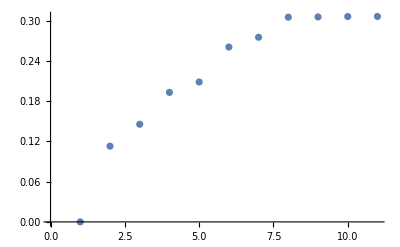

```mathematica
ListPlot[Table[Mean[differences038[[i]]],{i,1,11}]]
```

## Logging training on full MNIST set

### Net construction and logging

```mathematica
(* Defining a log to record weights, gradients, batch loss, and validation loss at training checkpoints. *)
logFileAll = CreateFile[];
appendToLogAll := PutAppend[ <|"Weights" -> #Weights,
				"Gradients" -> #Gradients, "BatchLoss" -> #BatchLoss, "ValidLoss" -> #ValidationLoss|>, logFileAll ]&
```

```mathematica
(* Training lenet on full MNIST set. Checkpointing occurs every 3 epochs. 
	NB: This took about 6 hours. *)
leNetTrainAll = NetTrain[
		lenet, 
		trainingData, 
		ValidationSet -> Scaled[0.1], 
		MaxTrainingRounds -> 100,
		BatchSize -> 100,
		TrainingProgressFunction -> {appendToLogAll, "Interval" -> Quantity[3, "Rounds"]}
	];
```

### Training full MNIST accuracy

```mathematica
(* Accuracy on full test set. *)
accuracyAll = ClassifierMeasurements[ leNetTrainAll, testData, "Accuracy" ]
```

0.9916

### Reading log full MNIST

```mathematica
(* Reading the checkpointing log. *)
logAll = ReadList[logFileAll];
```

```mathematica
(* Saving the net and log to disk. *)
Put[logAll, "2017_07_02_LogAll.mx"]
Export["2017_07_02_leNetTrainAll.wlnet",leNetTrainAll];
```

```mathematica
(* Get all weights at all training progress checkpoints (every 3 epochs). *) 
logAllW = Table[logAll[[i]]["Weights"],{i,Length[logAll]}];

(* Get all gradients at all training progress checkpoints (every 3 epochs). *) 
logAllG = Table[logAll[[i]]["Gradients"],{i,Length[logAll]}];
```

#### First conv. layer (1)

```mathematica
(* Among weights and gradients at each checkpoint, get the ones corresponding to the first (conv.) layer. *)
logAllW1W = Table[ logAllW[[i]][ {1, "Weights"} ], {i, Length[logAllW]}];
logAllG1W = Table[ logAllG[[i]][ {1, "Weights"} ], {i, Length[logAllG]}];
```

#### Second conv. layer (4)

```mathematica
(* Among weights and gradients at each checkpoint, get the ones corresponding to the 4th (conv.) layer. *)
logAllW4W = Table[ logAllW[[i]][ {4, "Weights"} ], {i, Length[logAllW]}];
logAllG4W = Table[ logAllG[[i]][ {4, "Weights"} ], {i, Length[logAllG]}];
```

#### First linear layer (8)

```mathematica
(* Among weights and gradients at each checkpoint, get the ones corresponding to the 8th (linear) layer. *)
logAllW8W = Table[ logAllW[[i]][ {8, "Weights"} ], {i, Length[logAllW]}];
logAllG8W = Table[ logAllG[[i]][ {8, "Weights"} ], {i, Length[logAllG]}];
```

#### Second linear layer (10)

```mathematica
(* Among weights and gradients at each checkpoint, get the ones corresponding to the 10th (linear) layer. *)
logAllW10W = Table[ logAllW[[i]][ {10, "Weights"} ], {i, Length[logAllW]}];
logAllG10W = Table[ logAllG[[i]][ {10, "Weights"} ], {i, Length[logAllG]}];
```

### Log full MNIST weight images

#### First conv. layer (1)

```mathematica
(* Turn the weights in the first layer into images. *)
logAllW1WImages = 
	Table[ 
		Map[
			Colorize[
				Image[
					Rescale[#, MinMax[logAllW1W], {0, 1}],
					Interleaving -> False, 
					ImageSize -> 20
				],
			(*ColorFunction -> ColorData["GrayTones"],*)
			ColorFunctionScaling -> False
		]&,
		logAllW1W[[i]]],
		{i, Length[logAllW1W]}
	];
```

Images of learned filters from first and last epoch of training on full MNIST set. Unlike for the 0, 3, 8 subset, we can see even with the human eye that the filters and changing.

```mathematica
Column[logAllW1WImages[[{1,33}]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Layer 1 filter difference plot

Here we log the differences in the images of the filters from epoch to epoch. There is indeed learning, and it follows a similar logarithmic curve to the 0, 3, 8 subset. The overall change in filters is greater than with the subset, however.

```mathematica
differencesAll = Table[
	Table[
		ImageDistance[logAllW1WImages[[1,i]],logAllW1WImages[[j,i]]],
	{i,Length[logAllW1WImages[[1]]]}]
	,{j,1,33}];
```

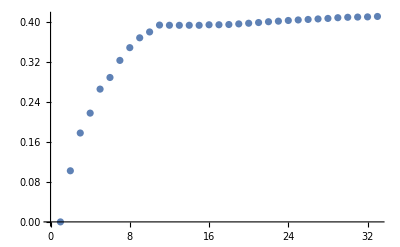

```mathematica
ListPlot[Table[Mean[differencesAll[[i]]],{i,1,33}]]
```

#### Second conv. layer (4)

```mathematica
dimAllW4W = Dimensions@logAllW4W
```

{33,50,20,5,5}

```mathematica
logAllW4W[[1,1]]
```

```mathematica
(* Turn the weights in the first layer into images. *)
logAllW4WImages = 
Column[ Table[
	Table[ 
		Map[
			Colorize[
				Image[
					Rescale[#, MinMax[logAllW4W], {0, 1}],
					Interleaving -> False, 
					ImageSize -> 20
				],
			(*ColorFunction -> ColorData["GrayTones"],*)
			ColorFunctionScaling -> False
		]&,
		logAllW4W[[j, All, i]]],
		{i, 20}
	], 
	{j, 1, 33}], Spacer[0.2]
];
```

$Aborted

```mathematica
Length@logAllW4WImages1
```

20

```mathematica
Column@logAllW4WImages1[[1;;5]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Turn the weights in the 4th layer into images. *)
logAllW4WImages = 
	Table[ 
		Map[
			Colorize[
				Image[
					Rescale[#, MinMax[logAllW4W], {0, 1}],
					Interleaving -> False, 
					ImageSize -> 20
				],
			(*ColorFunction -> ColorData["GrayTones"],*)
			ColorFunctionScaling -> False
		]&,
		logAllW4W[[i]][[All, j]]],
		{i, dimAllW4W[[1]]},
		{j, dimAllW4W[[3]]}
	];.
```

$Aborted

```mathematica
logAllW4WImages[[1]]
```

Images of learned filters from first and last epoch of training on full MNIST set. Unlike for the 0, 3, 8 subset, we can see even with the human eye that the filters and changing.

```mathematica
Column[logAllW4WImages[[{1,33}]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Log full MNIST convolved images

```mathematica
lenetLayers = {
	ConvolutionLayer[20, 5],
	Ramp,
	PoolingLayer[2, 2],
	ConvolutionLayer[50, 5],
	Ramp, 
	PoolingLayer[2, 2],
	FlattenLayer[],
	500,
	Ramp,
	10
	} (*,SoftmaxLayer[]}*);
```

```mathematica
netTable = Table[
			NetInitialize[
				NetChain[
					lenetLayers[[1 ;; i]],
					"Input" -> NetEncoder[{"Image", 28}],
					"Output" -> Automatic
				]
			],
			{i, Length[lenetLayers]}
		];
```

```mathematica
netTable[[7]][assoc1[[1,1]]]
```

{0.290843,0.532582,0.,0.339015,0.50164,0.260776,0.390431,0.348031,0.693486,0.,0.3858,0.0123901,0.,0.479787,0.0520704,0.,0.,0.,0.415713,0.,0.,0.330055,0.347284,0.,0.,0.258666,0.,0.,0.,0.,0.,0.,1.29361,1.34916,1.37392,0.992064,1.29913,1.19086,1.06413,1.1948,1.29312,1.11607,1.00643,1.41252,1.35982,1.48516,1.26275,1.42554,0.0140076,0.,0.194041,0.,0.0512963,0.147111,0.,0.620697,0.0397564,0.102443,0.353352,0.54928,0.240588,0.,0.477817,0.0853705,1.91341,1.84413,1.99594,2.15717,1.83193,1.78082,1.79902,1.9464,1.746,1.73395,1.98047,1.86106,1.7267,1.86254,1.64437,1.88027,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.12731,1.11133,1.14386,1.68187,1.1343,0.930261,1.18276,0.625823,1.01588,1.02307,0.967913,0.699628,1.11697,1.07936,0.562608,0.879129,0.40644,0.432697,0.201338,0.454015,0.462627,0.278363,0.,0.794671,0.448669,0.,0.575675,0.789604,0.,0.182164,0.795224,0.421403,1.5573,1.3775,2.42158,1.7137,1.47477,1.98451,1.99348,0.845294,1.50881,2.09199,1.22731,1.41321,1.91174,2.10569,1.00786,1.53961,2.57139,2.56395,2.32115,2.14773,2.59627,2.4093,2.05999,2.28798,2.47977,1.83101,2.10453,2.58633,1.68083,2.09775,2.52493,2.58292,0.,0.130165,0.,0.444812,0.0443399,0.,0.134081,0.369866,0.157698,0.092153,0.338307,0.164797,0.0877412,0.11476,0.557539,0.0894975,0.,0.,0.,0.0208881,0.,0.,0.,0.193444,0.,0.,0.,0.219694,0.0738603,0.,0.304101,0.,0.672148,0.474226,1.08184,0.69709,0.68658,0.738383,0.801247,0.278931,0.327783,0.913587,0.211709,0.713748,0.676712,0.80318,0.450189,0.747877,0.,0.,0.,0.00791353,0.,0.,0.,0.078944,0.,0.,0.175858,0.,0.0361259,0.,0.188566,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.314145,0.,0.,0.,0.146472,0.,0.,0.0131222,0.,0.,0.,0.264225,0.,1.05272,0.981811,0.785546,1.03567,1.03665,0.804823,1.49159,1.39362,0.932515,0.872127,1.50083,1.07483,0.872693,1.2424,1.44285,1.05595,0.730247,0.442063,0.240668,1.59827,0.619891,0.206683,0.763905,1.27263,0.442198,0.418322,1.25572,0.857851,0.270565,0.799377,1.17085,0.770621,0.,0.,0.312428,0.444355,0.,0.354575,0.293586,0.,0.,0.520066,0.251244,0.,0.0975114,0.218096,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.293592,0.28813,0.594475,0.138437,0.344146,0.359962,0.0689497,0.381456,0.425711,0.521296,0.330355,0.21491,0.779462,0.302123,0.404047,0.161641,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.187918,0.0892498,0.,0.25676,0.00981809,0.,0.154557,0.,0.,0.,0.,0.,0.,0.,0.603903,0.983623,1.06998,1.01147,0.890242,1.12039,0.926155,0.448136,1.00173,0.988717,0.901553,0.683994,0.92322,0.660253,0.54952,0.681497,1.61456,1.57798,1.43179,1.80805,1.60087,0.895741,1.65044,1.46804,1.34505,1.60449,1.6151,1.44126,1.17001,1.79127,1.39245,1.53659,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.110797,0.222901,0.188865,0.24835,0.170086,0.287433,0.,0.0966257,0.296067,0.,0.128863,0.218155,0.411382,0.0265811,0.1255,0.272643,0.0081885,0.352658,0.413133,0.,0.214392,0.548122,0.367133,0.295774,0.481326,0.649829,0.142291,0.236244,0.527339,0.0335772,0.27945,0.191631,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.61282,1.7272,1.55029,1.82409,1.70919,1.67611,1.59848,1.57116,1.72854,1.56609,1.37498,1.5016,1.71858,2.05269,1.48419,1.50448,0.439923,0.384817,1.07663,1.24088,0.295666,0.92581,0.99052,0.614592,0.562586,1.10069,0.66483,0.506591,1.0236,0.944692,0.549779,0.321785,1.15353,1.20387,1.20928,1.38851,1.1319,1.29973,1.1176,1.39461,1.20761,1.31936,1.23849,1.19552,1.57942,1.57905,1.33734,1.15917,0.187941,0.218766,0.,0.,0.21943,0.118209,0.,0.,0.154443,0.,0.,0.,0.,0.,0.151269,0.,0.168911,0.461171,0.,0.,0.420119,0.0702636,0.191435,0.105612,0.466124,0.,0.152243,0.,0.,0.0529497,0.,0.,1.00166,0.993128,0.97312,1.52386,1.02843,0.815616,0.888055,1.48367,0.980568,0.777931,1.22876,0.926778,0.756915,0.881984,1.16982,0.813906,0.349714,0.730472,0.736918,0.380315,0.5127,0.666072,0.267728,0.335428,0.659476,0.552402,0.220655,0.411359,0.569519,0.460574,0.52703,0.460034,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.13896,1.30843,1.21836,2.24447,1.14855,1.26053,2.1813,1.19804,1.22609,1.90099,2.15663,1.2887,1.10399,1.57627,1.34083,1.23786,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.63734,2.42945,2.98043,3.02602,2.63117,2.69601,2.69724,2.6566,2.42824,2.74305,2.56627,2.36384,2.66859,3.23254,2.50342,2.40315,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.248793,0.285162,0.224458,0.698207,0.263083,0.268101,0.51668,0.843353,0.418466,0.,0.830732,0.636686,0.0957345,0.70407,0.706035,0.257874,1.37432,1.6961,2.17703,1.5217,1.35473,2.27022,2.10777,1.04768,1.87395,2.38067,0.916982,1.18314,2.37915,1.89076,0.990544,1.38542,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.183219,0.,0.,0.0735308,0.,0.,0.115857,0.0988969,0.,0.,0.285751,0.,0.,0.463954,0.413518,0.619642,0.747579,0.372897,0.577914,0.670408,0.449552,0.469975,0.664038,0.55621,0.435589,0.611974,0.484569,0.342864,0.55995}

```mathematica
assoc1[[1]]
```

-Graphics-→1

```mathematica
trainRandSamp10 = RandomChoice[train10, 10];
```

```mathematica
Values[trainRandSamp10]
```

```mathematica
(* Displays progression through first 4 layers of first 10 training images (all 0's). 
	Convolved images shown, using 20 filters. *)

convolved10 =
Table[
	Table[
		Table[
			Image[out, ImageSize -> 20],
			{out, Take[[lenet10,i]][dataPoint]}
		],
		{dataPoint, train10[[1 ;; 2, 1]]}
	],
	{i, 6}
];
```

```mathematica
convolved0[[6]]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
convolved1 =
Table[
	Table[
		Table[
			Image[out, ImageSize -> 20],
			{out, netTable[[i]][dataPoint]}
		],
		{dataPoint, assoc1[[1 ;; 2, 1]]}
	],
	{i, 6}
];
```

```mathematica
flattened1 = 
	Table[
		Image@ImageAdjust[{netTable[[7]][dataPoint]}],
		{dataPoint, assoc1[[1;;4,1]]}
	]
```

ImageAdjust::imginv: Expecting an image or graphics instead of {{0.157515,0.474506,0.241857,0.209733,0.266281,0.28763,0.285177,0.,0.433879,0.228702,0.,«29»,0.,0.,0.574003,0.,0.0139177,0.745053,0.605217,0.,1.07251,1.02819,«750»}}.

Image::imgarray: The specified argument ImageAdjust[{{0.157515,0.474506,0.241857,0.209733,0.266281,0.28763,0.285177,0.,0.433879,«33»,0.574003,0.,0.0139177,0.745053,0.605217,0.,1.07251,1.02819,«750»}}] should be an array of rank 2 or 3 with machine-sized numbers.

ImageAdjust::imginv: Expecting an image or graphics instead of {{0.319675,0.241097,0.,0.0540277,0.419486,0.337464,0.,0.0336457,0.471141,0.220882,«31»,0.177525,0.254545,0.,0.,0.165061,0.220461,0.531545,1.03194,0.79167,«750»}}.

Image::imgarray: The specified argument ImageAdjust[{{0.319675,0.241097,0.,0.0540277,0.419486,0.337464,0.,0.0336457,0.471141,0.220882,«32»,0.254545,0.,0.,0.165061,0.220461,0.531545,1.03194,0.79167,«750»}}] should be an array of rank 2 or 3 with machine-sized numbers.

ImageAdjust::imginv: Expecting an image or graphics instead of {{0.304431,0.192558,0.134315,0.191781,0.302637,0.156902,0.0848063,0.089277,0.345171,«33»,0.201456,0.100948,0.,0.,0.20131,0.0661969,1.14945,1.09646,«750»}}.

General::stop: Further output of ImageAdjust::imginv will be suppressed during this calculation.

Image::imgarray: The specified argument ImageAdjust[{{0.304431,0.192558,0.134315,0.191781,0.302637,0.156902,0.0848063,0.089277,0.345171,«34»,0.100948,0.,0.,0.20131,0.0661969,1.14945,1.09646,«750»}}] should be an array of rank 2 or 3 with machine-sized numbers.

General::stop: Further output of Image::imgarray will be suppressed during this calculation.

{Image[ImageAdjust[{{0.157515,0.474506,0.241857,0.209733,0.266281,0.28763,0.285177,0.,0.433879,0.228702,0.,0.00685737,0.118371,0.0829701,0.,0.172373,0.737681,0.851544,0.833282,1.18219,0.859437,0.732145,0.815029,0.669794,0.74259,0.819859,0.594801,0.64852,0.302055,0.928159,0.548272,0.580774,0.,0.,0.,0.684207,0.,0.,0.149306,0.455364,0.,0.,0.574003,0.,0.0139177,0.745053,0.605217,0.,1.07251,1.02819,0.828453,1.28899,1.03555,0.816622,1.5811,1.15088,0.825077,1.2896,1.59267,1.2445,1.08216,1.59239,1.31962,1.17522,1.50947,1.32981,1.70193,1.7685,1.49103,1.5851,1.5942,1.85069,1.27191,1.83686,1.79653,1.2667,1.19425,2.23388,1.72464,1.50006,0.901877,0.609597,1.23129,0.617189,0.855508,1.43889,1.51127,1.09554,0.688386,1.24872,0.92648,1.10055,1.09363,0.716677,1.26455,1.09384,0.814026,0.76267,0.876368,0.723139,0.775111,0.990525,0.962166,0.586313,0.757982,1.26463,0.710597,0.916973,0.864133,1.28645,0.888478,0.881899,0.,0.,0.03788,0.,0.,0.,0.135932,0.,0.,0.241367,0.,0.,0.,0.200741,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.642416,0.78523,1.01387,1.13742,0.699914,0.735036,0.980294,1.41301,0.697229,0.786877,1.44502,1.02454,0.975278,1.17981,1.1415,0.886255,0.,0.,0.0946228,0.305125,0.,0.,0.32346,0.246212,0.,0.232308,0.164763,0.,0.,0.241026,0.,0.,0.,0.,0.,0.,0.,0.166664,0.136963,0.,0.,0.435863,0.,0.,0.,0.,0.,0.,0.341622,0.254469,0.486336,0.274305,0.308677,0.322233,0.488394,0.176705,0.128138,0.508139,0.438586,0.503535,0.287044,0.247236,0.,0.461747,0.882837,1.04612,0.516941,0.798931,1.03973,0.662125,0.592459,0.98962,1.07021,0.646849,0.662581,1.06294,0.74115,0.513634,1.11969,0.758538,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.56091,4.1032,4.35406,4.60716,4.51464,4.24066,3.92746,4.15727,3.96648,4.07649,3.90686,4.48876,4.18991,3.91363,4.18158,4.56562,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.542249,0.363242,0.601721,0.622094,0.422883,0.498417,0.613743,0.700857,0.399431,0.735482,0.91804,0.486359,0.345741,0.0870243,0.532585,0.590994,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.54124,1.13063,1.17548,0.547019,0.488466,1.53109,0.422889,0.724421,1.35567,1.08284,0.735247,0.694821,1.29356,0.329645,0.716608,0.750528,0.778859,1.2018,1.04092,0.91336,0.81483,0.992911,0.967403,0.500187,1.02833,0.849336,0.638722,0.651772,1.10951,1.06048,0.734749,0.707869,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.92184,1.91076,1.87532,1.68825,1.93636,1.97398,1.61294,1.62841,1.95729,1.66501,1.02099,1.9182,2.18679,1.74871,1.69698,1.92783,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0334361,0.120396,0.,0.00389642,0.,0.181633,0.,0.131444,0.134046,0.161661,0.108987,0.0357708,0.038688,0.105591,1.50187,1.48106,1.5821,1.36337,1.46632,1.19492,1.28721,1.95368,1.34733,1.40001,2.05321,1.74707,1.02203,1.5078,2.11183,1.54975,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.61835,1.58749,1.87349,1.77222,1.56255,2.12851,1.84269,1.86872,1.6654,2.17804,1.96546,1.6762,2.38237,2.18656,2.05866,1.62636,0.,0.313829,0.293975,0.222627,0.297069,0.224447,0.,0.,0.330424,0.,0.,0.,0.0821858,0.,0.,0.,2.1338,2.32187,1.77871,2.0267,2.32001,1.96954,1.76767,1.60445,2.21551,1.67676,1.78362,1.87235,1.78597,2.03993,1.96425,1.86084,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.39461,1.42251,1.3644,0.971543,1.41475,1.45841,0.743324,1.77997,1.49014,1.12524,1.48921,1.86148,1.26543,0.88388,1.69586,1.42908,0.,0.,0.,0.262629,0.,0.,0.21545,0.,0.,0.144051,0.,0.,0.,0.0858845,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.6462,2.5992,2.10915,2.74646,2.58745,2.22424,2.27277,2.6474,2.25687,2.50217,2.2812,2.37389,2.30799,2.18113,2.33647,2.50738,0.,0.,0.176189,0.41148,0.,0.0114248,0.524658,0.737975,0.0870107,0.,0.612965,0.114395,0.,0.662096,0.243217,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.98729,2.07567,2.02033,2.33821,2.06668,1.9243,1.95919,1.95128,2.0176,1.76335,1.92973,2.02501,1.9813,1.96677,1.91935,2.09344,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.8861,1.76456,2.1602,2.57307,1.79254,1.76551,2.15955,1.87596,1.80877,2.07424,2.0923,1.85775,1.81913,2.21338,2.25244,1.80467,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}]],Image[ImageAdjust[{{0.319675,0.241097,0.,0.0540277,0.419486,0.337464,0.,0.0336457,0.471141,0.220882,0.180666,0.161885,0.44709,0.326184,0.321444,0.,0.693573,1.45669,1.21678,0.592118,0.559936,0.721101,1.64815,0.688077,0.488285,0.75498,1.5865,0.787101,0.583433,0.223155,0.76182,0.613529,0.218464,0.,0.,0.,0.0671259,0.,0.3761,0.0164223,0.,0.177525,0.254545,0.,0.,0.165061,0.220461,0.531545,1.03194,0.79167,1.27286,1.23524,1.07868,0.815547,1.30034,1.30402,1.13026,0.596153,1.02091,1.25299,1.10147,0.60391,0.686703,1.20101,1.34857,1.44889,1.92365,1.50924,1.39942,1.67417,1.98204,1.43489,1.41252,1.70051,1.89815,1.35421,1.43156,1.54464,1.5256,1.43592,1.13902,0.470557,1.09796,1.00365,1.00295,0.494244,0.866396,1.20753,0.925751,0.561409,0.772976,1.18433,1.12677,1.31039,0.717592,0.955037,0.787194,0.797591,1.25528,0.646337,0.746071,0.692602,1.24516,0.678658,0.749784,0.747197,1.19004,0.572936,0.820097,0.810748,1.22769,0.943287,0.,0.,0.205205,0.,0.,0.,0.283309,0.,0.,0.,0.228055,0.17332,0.,0.,0.336631,0.310287,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.639579,0.992423,1.24341,1.1976,0.594168,1.47974,1.0009,1.15707,0.741734,1.5363,1.18045,1.2674,0.614811,1.16603,1.27053,1.19604,0.,0.,0.0657029,0.,0.,0.,0.165107,0.,0.,0.,0.101736,0.,0.,0.,0.,0.,0.,0.0694257,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.295432,0.100837,0.725456,0.500422,0.320756,0.080314,0.738125,0.671727,0.26333,0.0814075,0.533257,0.699183,0.297208,0.,0.,0.461671,0.796271,0.73392,1.23115,1.38288,1.02228,0.200437,1.03272,1.47693,1.18507,0.249849,1.01909,1.60472,1.08803,0.928846,0.87355,1.36541,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.3724,4.02533,4.19817,4.60793,4.50929,3.40965,3.19262,4.56457,4.52096,3.50398,3.15754,4.50681,4.58637,3.48945,3.19279,4.46714,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.412028,0.49346,0.845851,0.964784,0.512158,0.308576,0.442727,0.775969,0.643517,0.482254,0.361093,0.769442,0.634041,0.425838,0.154778,0.633449,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.768599,0.57094,0.358509,0.721563,0.761148,0.842775,0.480255,0.722576,0.581979,0.908865,0.736154,0.688585,0.657622,1.10304,0.693349,0.589396,0.968314,0.954943,0.284759,0.732086,0.822683,0.949324,0.591879,0.581853,0.881215,0.978867,0.931709,0.556472,0.845351,1.10017,1.15681,0.502328,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.12812,1.72558,1.45201,1.79555,1.95081,1.93944,1.53103,1.71897,1.97209,1.99107,1.58598,1.58049,2.01432,2.21406,1.87182,1.51158,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00388993,0.440742,0.263818,0.108763,0.,0.475581,0.344821,0.157111,0.,0.0686769,0.220296,0.339818,0.0390277,0.235338,0.239246,0.,1.4795,1.39391,1.85552,1.7105,1.43266,1.2696,1.91522,1.55021,1.61929,1.37927,1.88406,1.5358,1.57412,1.14507,1.6402,1.59783,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.61569,1.6661,1.78375,1.68227,1.77394,1.64293,1.78258,1.65092,1.80796,1.5387,1.67709,1.70038,1.9992,2.0285,1.87052,1.78983,0.,0.121692,0.205263,0.,0.,0.125487,0.183394,0.,0.,0.115229,0.,0.,0.,0.,0.,0.,2.38643,1.62723,2.15894,1.64595,2.56192,1.57622,2.03978,1.87155,2.51428,1.89614,1.57034,2.00669,1.94913,2.01049,1.63511,2.1445,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0342606,0.08788,0.,0.,0.0416877,0.335254,0.,0.,0.0305592,0.220938,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0282943,0.,1.34224,1.38869,1.04882,1.31454,1.32044,1.62961,1.39108,1.16004,1.3456,1.50818,1.42736,1.03378,1.37137,0.912604,1.22738,1.02311,0.,0.,0.,0.,0.,0.,0.165752,0.,0.,0.,0.377974,0.,0.,0.,0.184798,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.17946,2.62044,2.32123,2.25702,2.43549,2.52102,1.72187,2.15085,2.44412,2.65356,1.86662,2.17303,2.47082,2.4026,2.20246,2.53277,0.,0.365662,0.218769,0.,0.,0.271461,0.172115,0.,0.,0.221656,0.313336,0.,0.,0.11836,0.58049,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.14774,1.93134,2.11264,2.06806,1.91744,1.65886,1.80673,2.09674,2.12324,1.66872,1.81664,2.16356,1.96125,1.81871,1.83703,2.13364,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.93694,2.30163,1.87137,2.02386,1.99728,1.3012,2.28221,2.12022,1.91024,1.20508,2.33498,2.01804,1.96306,1.21688,2.36992,1.99719,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}]],Image[ImageAdjust[{{0.304431,0.192558,0.134315,0.191781,0.302637,0.156902,0.0848063,0.089277,0.345171,0.130831,0.138033,0.303011,0.302416,0.132811,0.256873,0.307205,0.783283,1.01113,1.10019,0.679721,0.59344,0.796619,1.15711,0.76544,0.527443,0.733545,0.966925,0.858378,0.547897,0.57416,0.866596,0.777139,0.,0.,0.104088,0.,0.0446462,0.,0.0561086,0.,0.0483715,0.,0.201456,0.100948,0.,0.,0.20131,0.0661969,1.14945,1.09646,1.18983,1.15551,1.13403,1.19676,1.2202,1.13187,1.09173,0.986403,1.17248,1.20351,1.07052,1.08013,1.00455,1.2045,1.42008,1.50054,1.88012,1.58741,1.39729,1.71297,2.4287,1.46174,1.40109,1.66634,2.40934,1.35976,1.45436,1.60458,2.20342,1.3033,0.898715,0.724724,0.704105,0.938659,0.941305,0.799854,0.777578,1.02985,0.911242,0.908108,0.68157,1.05584,1.07324,1.22744,0.783714,1.03155,0.903083,0.474058,1.19953,0.838028,0.759199,0.672265,1.12485,0.763029,0.775621,1.06377,1.22267,0.855736,0.794199,1.17246,1.2236,0.848507,0.,0.,0.,0.,0.,0.,0.0957089,0.,0.,0.,0.0757149,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.708571,1.2871,1.18069,1.04445,0.656175,1.46932,1.25971,1.00247,0.650914,1.37128,1.26806,0.77474,0.649916,1.26561,1.0612,0.898573,0.,0.,0.157334,0.,0.,0.,0.184947,0.,0.,0.,0.0326211,0.,0.,0.,0.128353,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0855959,0.,0.294667,0.459787,0.487656,0.460091,0.287392,0.277283,0.383958,0.466022,0.300437,0.419841,0.207219,0.53248,0.310998,0.506344,0.0411877,0.518843,0.823562,0.758381,1.00213,0.968875,1.19953,0.603789,1.05605,0.998505,1.09639,0.422502,0.96169,1.05775,0.904998,0.623019,0.920316,0.968794,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.46029,4.57259,4.52557,4.55031,4.49949,4.24867,3.92377,4.51138,4.53908,4.01692,3.92666,4.5727,4.5721,4.16828,4.20815,4.52182,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.560492,0.923384,0.527938,0.775811,0.582546,0.882277,0.663886,0.588397,0.609969,0.60666,0.6579,0.532268,0.593919,0.564425,0.588892,0.592416,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.621927,0.971242,0.183706,0.674249,0.551966,0.930875,0.753324,0.702211,0.558221,0.743945,1.2693,0.709959,0.721982,0.622505,1.39263,0.768533,0.889349,1.13063,0.75754,0.722449,0.881345,0.986521,0.756431,0.638051,0.84394,1.33343,0.464967,0.627948,0.812991,1.20402,0.784195,0.723819,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0533519,0.,0.,0.,0.0430076,0.,0.,0.,0.,0.,0.,0.,0.,1.95801,2.15326,1.98078,1.90307,1.97862,1.88984,1.70329,1.86734,1.95446,1.99515,1.75429,1.76817,2.0588,1.9352,1.70483,1.64573,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.158142,0.286303,0.,0.,0.199274,0.189967,0.0124632,0.,0.130895,0.0542801,0.131811,0.,0.,0.0640881,0.234287,1.49531,1.66188,1.66183,1.60968,1.53086,1.64103,2.11297,1.50775,1.56923,1.27378,2.19735,1.53077,1.53227,1.16882,2.02031,1.46722,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.69653,2.11859,1.8663,1.77004,1.83011,1.77493,1.93839,1.90302,1.77715,2.07677,2.34578,1.71415,1.75648,2.31734,2.57243,1.80664,0.,0.,0.131145,0.,0.0683025,0.,0.194088,0.,0.0502365,0.,0.245267,0.,0.,0.,0.13488,0.,2.5131,1.9293,1.73498,1.77658,2.52686,1.61573,2.08145,2.04276,2.16895,2.15502,2.06888,2.22961,1.9318,2.2994,1.79774,2.19605,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.30489,1.53028,1.46548,1.3547,1.30685,1.18675,1.75264,1.29458,1.32526,1.10843,1.62329,1.26314,1.3627,1.03086,1.57656,1.3532,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.38834,2.56306,2.35161,2.43206,2.414,2.67004,2.10512,2.42786,2.41603,2.9265,2.19237,2.42945,2.47583,2.4881,2.24987,2.68179,0.,0.0413584,0.,0.,0.,0.175179,0.127333,0.,0.,0.203762,0.245228,0.,0.,0.0650363,0.161146,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.12848,2.15471,2.25166,1.96981,2.14786,1.83097,2.17496,2.09627,2.16736,1.96722,2.06337,2.10928,1.96308,2.07686,2.09724,2.16237,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.91487,2.13094,1.95953,2.07771,1.92985,1.6201,2.32691,2.21152,1.90267,1.60572,2.34047,2.38733,1.91445,1.58732,2.5148,2.43209,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}]],Image[ImageAdjust[{{0.226963,0.183958,0.110104,0.153352,0.473827,0.155829,0.182308,0.153831,0.458544,0.176377,0.,0.0744583,0.388909,0.233555,0.,0.185652,0.833511,0.923733,1.0043,0.637882,0.557845,0.764664,1.23471,0.81879,0.559773,0.710099,1.10024,0.74856,0.529309,0.570279,0.980849,0.87994,0.,0.,0.,0.,0.,0.,0.190371,0.,0.,0.,0.123181,0.,0.,0.,0.148651,0.,1.11569,1.02722,1.25183,1.20379,1.04073,1.08817,1.16528,1.11549,1.09436,1.26163,1.16894,1.11432,1.12842,1.25633,0.982012,1.0929,1.41096,1.50795,1.77137,1.45148,1.4218,1.55572,1.83004,1.48327,1.40576,1.76673,2.02708,1.40837,1.37892,1.99125,2.14817,1.49271,0.997616,0.629597,0.687037,0.970556,0.94412,0.896598,0.681028,1.0048,0.896856,0.959204,0.621617,1.02687,0.898906,0.992523,0.58402,0.956832,1.18203,0.607524,1.23387,0.813498,0.83601,0.550187,1.35327,0.82851,0.9159,0.423212,1.16712,0.833213,0.889716,0.643666,1.10026,0.887622,0.,0.,0.,0.,0.,0.,0.0650173,0.,0.,0.,0.0734406,0.,0.,0.,0.030608,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.638683,0.941923,1.05259,1.06961,0.647092,1.25413,0.982992,0.987748,0.64385,1.38255,1.00738,1.1102,0.651732,1.42212,1.0975,0.966326,0.,0.,0.106609,0.,0.,0.,0.0182669,0.,0.,0.,0.198804,0.,0.,0.,0.126152,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.326317,0.564305,0.659529,0.429765,0.256311,0.314761,0.551675,0.365883,0.282499,0.387866,0.349195,0.432826,0.287735,0.308721,0.242571,0.414141,0.787124,0.710432,1.0195,0.946103,1.09567,0.669299,1.02516,1.15363,1.23649,0.751602,0.913655,1.0106,1.17847,0.556698,1.02388,0.988001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.40344,4.31069,4.6986,4.57883,4.46505,4.01817,3.93581,4.52726,4.45677,4.13042,3.87589,4.50794,4.48154,4.26906,3.99788,4.52318,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.467074,0.656296,0.834643,0.759661,0.473004,0.776693,0.514341,0.612952,0.519317,1.11193,0.449456,0.627124,0.61309,1.06299,0.4138,0.610056,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.716157,0.919293,0.455356,0.67894,0.644366,0.887345,0.302859,0.65785,0.537023,0.979564,0.415184,0.624147,0.583247,0.851239,0.541119,0.582803,0.975543,1.22529,0.732671,0.740463,0.843116,1.00359,0.904963,0.707265,0.889607,0.934409,0.902593,0.709114,0.866526,1.04007,0.994417,0.724197,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.0352,2.00945,1.76379,1.92289,1.97576,2.26758,1.82231,1.92672,1.9318,2.23861,1.74886,1.89592,1.97663,2.07709,1.71554,1.94133,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.361028,0.425211,0.150907,0.,0.245939,0.196217,0.0663754,0.,0.165514,0.162128,0.0754384,0.,0.1622,0.118847,0.0719294,1.47746,1.71784,1.65749,1.57656,1.47016,1.66297,1.78617,1.61873,1.47765,1.8101,1.90147,1.52979,1.57483,1.72625,2.11868,1.53273,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.93985,2.31953,1.57732,1.65247,1.9063,2.18018,1.59845,1.72618,1.94903,2.05582,1.76471,1.77631,2.15076,1.90907,1.84863,1.83793,0.,0.,0.144256,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0299478,0.,0.,0.,2.52733,1.75648,1.79251,1.78777,2.56001,1.53238,2.06905,1.81499,2.60993,1.59115,2.19668,1.86121,2.61627,1.61004,2.07554,1.90611,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0727313,0.,0.,0.,0.124262,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.331,1.4139,1.4148,1.34126,1.35724,1.4049,1.62821,1.34704,1.32333,1.19829,1.81165,1.29788,1.29992,1.07758,1.97449,1.32487,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.39503,2.56923,2.3726,2.46405,2.43652,2.39617,2.3461,2.38849,2.45512,2.43057,2.38573,2.41493,2.40977,2.49538,2.37492,2.48704,0.,0.0719293,0.,0.,0.,0.15037,0.,0.,0.,0.000826746,0.00677535,0.,0.,0.135838,0.236884,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.06075,2.28774,2.0601,1.99122,2.14389,1.71681,1.90307,2.0135,1.97796,1.76042,1.91232,2.05415,2.24487,1.8689,2.13281,2.0228,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.01875,2.07343,2.02932,1.88149,1.98279,1.59071,2.28693,1.98141,1.9241,1.63071,2.17533,1.98721,1.88087,1.53997,2.43856,2.16641,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}]]}

```mathematica
Dimensions[convolved1[[6]]]
```

{2,50}

```mathematica
convolved0[[6]]convolved1[[6]]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

FIND WEIGHTS ON THESE!